## Hilbert space

```mathematica
(*4LS dimension and basis vectors*)
dim4LS = 4;
{trionUp, trionDw, spinUp,spinDw} =Table[ Basis[dim4LS,i], {i,1,4}] ;

(*Defines a single Fock space*)
dimFock =4; (*80; This works for 10 photons*)

totaldimension = dimFock^2 dim4LS;
numberState[n_]:=Basis[dimFock,n+1];
LoadBosonicOperators[dimFock];
ℐFock=Eye[dimFock];

(*Polarization dipole vectors*)
ΣR = out[spinUp,trionUp]//mf;
ΣL = out[spinDw,trionDw]//mf;
ΣH = (ΣR + ΣL)/(√2);
ΣV=ⅇ^(ⅈ π/2)((ΣR - ΣL)/(√2));
ΣA=ⅇ^(-ⅈ π/4)((ΣR - ⅈ ΣL)/(√2));
ΣD=ⅇ^(ⅈ π/4)((ΣR + ⅈ ΣL)/(√2));

(*Total polarization dipole vectors*)
σR=kron[ΣR,ℐFock,ℐFock];
σL=kron[ΣL,ℐFock,ℐFock];
σH =kron[ΣL,ℐFock,ℐFock];
σV =kron[ΣL,ℐFock,ℐFock];
σA =kron[ΣL,ℐFock,ℐFock];
σD =kron[ΣL,ℐFock,ℐFock];

(*Defining virtual cavity right and Left bosonic operators*)
𝕒R=kron[Eye[4],a,ℐFock];
𝕒L=kron[Eye[4],ℐFock,a];
𝕒H=(𝕒R + 𝕒L)/(√2);
𝕒V=ⅇ^(ⅈ π/2)((𝕒R - 𝕒L)/(√2));
𝕒A=ⅇ^(-ⅈ π/4)((𝕒R - ⅈ 𝕒L)/(√2));
𝕒D=ⅇ^(ⅈ π/4)((𝕒R + ⅈ 𝕒L)/(√2));

(*Pauli-sh operators in the spin subspace - esc-scs-esc.*)
𝓈x = kron[out[spinUp,spinDw]+out[spinDw,spinUp],ℐFock,ℐFock];
𝓈y =kron[ -ⅈ out[spinUp,spinDw]+ⅈ out[spinDw,spinUp],ℐFock,ℐFock];
𝓈z = kron[out[spinUp,spinUp] - out[spinDw,spinDw],ℐFock,ℐFock];
𝓈m = kron[out[spinDw, spinUp],ℐFock,ℐFock];

𝓈vec = {𝓈x,𝓈y,𝓈z};

(*Pauli-sh operators in the trion subspace- esc-dss-esc.*)
𝕤x = kron[out[trionUp,trionDw]+out[trionDw,trionUp],ℐFock,ℐFock];
𝕤y = kron[-ⅈ out[trionUp,trionDw]+ⅈ out[trionDw,trionUp],ℐFock,ℐFock];
𝕤z = kron[out[trionUp,trionUp] - out[trionDw,trionDw],ℐFock,ℐFock];
𝕤m = kron[out[trionDw, trionUp],ℐFock,ℐFock];
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0)

## Protocol

```mathematica
(*Applying the first Beam splitter (BS)*)
(*Upper path*)
uL = Cos[θ1] 𝕒L;
uR = Cos[θ1] 𝕒R;

(*Down path*)
dL = ⅈ Sin[θ1] 𝕒L;
dR = ⅈ Sin[θ1] 𝕒R;
```

```mathematica
(*Defining the hamiltonian and light-matter interaction for the upper path*)
H0upper = ΔL σL†.σL+ΔR σR†.σR ;(*Δ's are the detunings relative to the source*)
Hintupper = -(ⅈ √ηlm √(γ η κ))/2(σL†.uL-uL†.σL+σR†.uR - uR†.σR);
Hupper = H0upper + Hintupper;
```

```mathematica
(*Defining the output modes*)
Luout = √ηd(√γ σL + √(κ η)uL);
Ruout = √ηd(√γ σR + √(κ η)uR);
Ldout = √ηd( √(κ η)dL);
Rdout = √ηd(√(κ η)dR);
```

```mathematica
(*Interference at the 2nd BS*)
(*Output field directed to the detector 1*)
RoutD1 = Ruout Cos[θ2] + ⅈ Exp[ⅈ ϕ]Rdout Sin[θ2];
LoutD1 = Luout Cos[θ2] + ⅈ Exp[ⅈ ϕ]Ldout Sin[θ2];

(*Output field routed to the detector 2*)
RoutD2 = Rdout Exp[ⅈ ϕ] Cos[θ2] + ⅈ Ruout Sin[θ2];
LoutD2 = Ldout Exp[ⅈ ϕ] Cos[θ2] + ⅈ Luout Sin[θ2];
```

```mathematica
(*Vectorized superoperators*)
PrettyTiming[

ℋ = UnitaryToVec@Hupper;
(*System decay channels with correlation due to cascaded coupling*)
𝒟γ = LindbladToVec[Luout] + LindbladToVec[Ruout]+LindbladToVec[Ldout] + LindbladToVec[Rdout]+(1-η)κ (LindbladToVec[𝕒R]+LindbladToVec[𝕒L]);
(* System (γs) and input field (κs) dephasing *)
𝒟γs = γs LindbladToVec[σL†.σL]+γs LindbladToVec[σR†.σR]+κs LindbladToVec[𝕒L†.𝕒L]+κs LindbladToVec[𝕒R†.𝕒R];

(*Conditional evolution: jump operators at the detector.*)
𝒥ηd = -ηRD1 JumpOp[RoutD1]-ηRD2 JumpOp[RoutD2]-ηLD1 JumpOp[LoutD1]-ηLD2 JumpOp[LoutD2];
]
```

0h : 0m : 1s

```mathematica
ℒ = ℋ+𝒟γ+𝒟γs+𝒥ηd;
```

```mathematica
Dimensions@ℒ
Head@ℒ
```

{4096,4096}

SparseArray

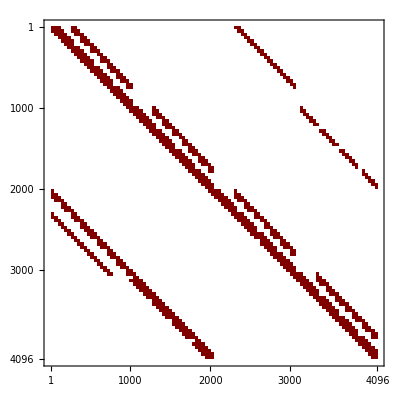

```mathematica
MatrixPlot@ℒ
```

### Fock-Liouville space exploration

Choose a parameter set to explore the Fock-Liouville space:

```mathematica
par={ΔL->0,ΔR->0, (* Detunings *)γ->1,κ->0.01,(* Decay rates *)η->0.9,ηlm->0.9,ηd->0.9,(* Input/coupling efficiency *)
ηRD1->0.5,ηRD2->0.5,ηLD1->0.5,ηLD2->0.5,(* Detector efficiency/conditional evolution parameters *)γs->0.1,κs->0.1,(* Dephasing *)ϕ->0.235,(* interferometer phase *)θ1->0.412,θ2->0.12(* Beam splitter ratios *)};
```

```mathematica
(* Choose an initial state to reduce the necessary subspace: gs spin superposition + H-polarized input coherent state (up to 3 photons) *)(*gs spin superposition*)
spinUp+spinDw//mf;(*My ordering is different from Stephen's one.*)
CoherentState[1]//N//mf;
```

(0
0
1
1)

(0.606531
0.606531
0.428882
0.247615)

```mathematica
test1=Flatten@KroneckerProduct[{0,0,1,1},{1,1,1,1},{1,0,0,0}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}

```mathematica
test11 = Flatten@KroneckerProduct[test1,test1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
test2=kron[{0,0,1,1},{1,1,1,1},{1,0,0,0}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}

```mathematica
kron[test,test]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
istate=kron[{0,0,1,1},{1,1,1,1},{1,0,0,0}];
istate=kron[istate,istate];
```

```mathematica
aux1 = Sign[istate]*Range[totaldimension^2];(*Sign of initial state assigns 1 to positive values, 0 when the value is 0 and -1 when the value is negative. Range[Dim2] makes a big list going from 1 to 4096. The output is a list with a bunch of zeros and the indexes of the initial nodes where the values are not zero.*)
```

```mathematica
initialnodes=DeleteCases[aux1,0];(*every place where the value of aux 1 is zero are neglected*)
```

```mathematica
initialnodes
```

{2081,2085,2089,2093,2097,2101,2105,2109,2337,2341,2345,2349,2353,2357,2361,2365,2593,2597,2601,2605,2609,2613,2617,2621,2849,2853,2857,2861,2865,2869,2873,2877,3105,3109,3113,3117,3121,3125,3129,3133,3361,3365,3369,3373,3377,3381,3385,3389,3617,3621,3625,3629,3633,3637,3641,3645,3873,3877,3881,3885,3889,3893,3897,3901}

```mathematica
Head@%
Dimensions@%%
```

List

{64}

```mathematica
aux2= NumericQ/@Vec[ℒ+x*Eye[Length[ℒ]]]
```

SparseArray[…]

```mathematica
aux2[[2]]
```

True

```mathematica
aux22= Table[aux2[[i]]/.False->0/.True->1,{i,1,Length@aux2}]
```

SparseArray[…]

```mathematica
Head@%
Dimensions@%%
```

SparseArray

{16777216}

```mathematica
adjacencymatrix=Partition[aux2,totaldimension^2];
```

```mathematica
Head@%
Dimensions@%%
```

SparseArray

{4096,4096}

```mathematica
aux3=Transpose[Sign[adjacencymatrix+Transpose[adjacencymatrix]]]
```

SparseArray[<26624>, {4096, 4096}, Sign[True]]

```mathematica
Head@%
Dimensions@%%
```

SparseArray

{4096,4096}

```mathematica
GraphPlot[aux3,
VertexStyle->Table[i->If[MemberQ[initialnodes,Range[totaldimension^2][[i]]],Red,Black],{i,totaldimension^2}],
PlotLabel->"Full Fock-Liouville space and intereactions for the ME",
Frame->True,
FrameLabel->{"Red dot is the initial state"}]
```

GraphPlot[SparseArray[<26624>, {4096, 4096}, Sign[True]],VertexStyle→{1→GrayLevel[0],2→GrayLevel[0],3→GrayLevel[0],4→GrayLevel[0],5→GrayLevel[0],6→GrayLevel[0],7→GrayLevel[0],8→GrayLevel[0],9→GrayLevel[0],10→GrayLevel[0],11→GrayLevel[0],12→GrayLevel[0],13→GrayLevel[0],14→GrayLevel[0],15→GrayLevel[0],4066,4082→GrayLevel[0],4083→GrayLevel[0],4084→GrayLevel[0],4085→GrayLevel[0],4086→GrayLevel[0],4087→GrayLevel[0],4088→GrayLevel[0],4089→GrayLevel[0],4090→GrayLevel[0],4091→GrayLevel[0],4092→GrayLevel[0],4093→GrayLevel[0],4094→GrayLevel[0],4095→GrayLevel[0],4096→GrayLevel[0]},PlotLabel→56,Frame→True,FrameLabel→{Red dot is the initial state}]
 |  |  |  |

```mathematica
rowsℒ = Length@ℒ;
colsℒ = Length@ℒ[[1]];
```

```mathematica
PrettyTiming[ℒtest = SparseArray@Table[ℒ[[r,c]]/.par,{r,1,rowsℒ},{c,1,colsℒ}]]
```

0h : 0m : 27s

SparseArray[<18428>, {4096, 4096}]

```mathematica
expState=Sign[Abs[MatrixExp[ℒtest].istate]];
```

```mathematica
Dimensions@%
Head@%%
```

{4096}

List

```mathematica
aux4=expState*Range[totaldimension^2];
```

```mathematica
(* Let's now look at all the Fock-Liouville basis vectors that were explored *)
nodeset=DeleteCases[aux4,0];
```

```mathematica
nodeset
```

{1,5,9,33,37,41,45,49,53,57,61,257,261,265,289,293,297,301,305,309,313,317,513,517,521,545,549,553,557,561,565,569,573,2049,2053,2057,2081,2085,2089,2093,2097,2101,2105,2109,2305,2309,2313,2337,2341,2345,2349,2353,2357,2361,2365,2561,2565,2569,2593,2597,2601,2605,2609,2613,2617,2621,2817,2821,2825,2849,2853,2857,2861,2865,2869,2873,2877,3073,3077,3081,3105,3109,3113,3117,3121,3125,3129,3133,3329,3333,3337,3361,3365,3369,3373,3377,3381,3385,3389,3585,3589,3593,3617,3621,3625,3629,3633,3637,3641,3645,3841,3845,3849,3873,3877,3881,3885,3889,3893,3897,3901}

```mathematica
aux5=Transpose[Sign[adjacencymatrix+Transpose[adjacencymatrix]]]
```

SparseArray[<26624>, {4096, 4096}, Sign[True]]

```mathematica
Head@%
Dimensions@%%
```

SparseArray

{4096,4096}

```mathematica
aux6 = aux5[[nodeset,nodeset]]
```

SparseArray[…]

```mathematica
aux66 = Normal@aux6
```

{{Sign[False],Sign[True],Sign[True],Sign[True],Sign[False],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],100,Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True],Sign[True]},120}
 |  |  |  |

```mathematica
AdjacencyGraph[aux6,
VertexStyle->Table[i->If[MemberQ[initialnodes,nodeset[[i]]],Red,Black],{i,Length[nodeset]}],PlotLabel->"Necessary Fock-Liouville subspace for the ME evolution",
Frame->True,
FrameLabel->{"Red dots are the initial state"}]
```

AdjacencyGraph::inv: The argument SparseArray[Automatic,«3»] in … is not a valid adjacency matrix.

AdjacencyGraph[Automatic,SparseArray[…],VertexStyle→{1→GrayLevel[0],2→GrayLevel[0],3→GrayLevel[0],4→GrayLevel[0],5→GrayLevel[0],6→GrayLevel[0],7→GrayLevel[0],8→GrayLevel[0],9→GrayLevel[0],10→GrayLevel[0],11→GrayLevel[0],12→GrayLevel[0],13→GrayLevel[0],14→GrayLevel[0],15→GrayLevel[0],16→GrayLevel[0],17→GrayLevel[0],18→GrayLevel[0],19→GrayLevel[0],20→GrayLevel[0],21→GrayLevel[0],22→GrayLevel[0],23→GrayLevel[0],24→GrayLevel[0],25→GrayLevel[0],26→GrayLevel[0],27→GrayLevel[0],28→GrayLevel[0],29→GrayLevel[0],30→GrayLevel[0],31→GrayLevel[0],32→GrayLevel[0],33→GrayLevel[0],34→GrayLevel[0],35→GrayLevel[0],36→GrayLevel[0],37→RGBColor[1, 0, 0],38→RGBColor[1, 0, 0],39→RGBColor[1, 0, 0],40→RGBColor[1, 0, 0],41→RGBColor[1, 0, 0],42→RGBColor[1, 0, 0],43→RGBColor[1, 0, 0],44→RGBColor[1, 0, 0],45→GrayLevel[0],46→GrayLevel[0],47→GrayLevel[0],48→RGBColor[1, 0, 0],49→RGBColor[1, 0, 0],50→RGBColor[1, 0, 0],51→RGBColor[1, 0, 0],52→RGBColor[1, 0, 0],53→RGBColor[1, 0, 0],54→RGBColor[1, 0, 0],55→RGBColor[1, 0, 0],56→GrayLevel[0],57→GrayLevel[0],58→GrayLevel[0],59→RGBColor[1, 0, 0],60→RGBColor[1, 0, 0],61→RGBColor[1, 0, 0],62→RGBColor[1, 0, 0],63→RGBColor[1, 0, 0],64→RGBColor[1, 0, 0],65→RGBColor[1, 0, 0],66→RGBColor[1, 0, 0],67→GrayLevel[0],68→GrayLevel[0],69→GrayLevel[0],70→RGBColor[1, 0, 0],71→RGBColor[1, 0, 0],72→RGBColor[1, 0, 0],73→RGBColor[1, 0, 0],74→RGBColor[1, 0, 0],75→RGBColor[1, 0, 0],76→RGBColor[1, 0, 0],77→RGBColor[1, 0, 0],78→GrayLevel[0],79→GrayLevel[0],80→GrayLevel[0],81→RGBColor[1, 0, 0],82→RGBColor[1, 0, 0],83→RGBColor[1, 0, 0],84→RGBColor[1, 0, 0],85→RGBColor[1, 0, 0],86→RGBColor[1, 0, 0],87→RGBColor[1, 0, 0],88→RGBColor[1, 0, 0],89→GrayLevel[0],90→GrayLevel[0],91→GrayLevel[0],92→RGBColor[1, 0, 0],93→RGBColor[1, 0, 0],94→RGBColor[1, 0, 0],95→RGBColor[1, 0, 0],96→RGBColor[1, 0, 0],97→RGBColor[1, 0, 0],98→RGBColor[1, 0, 0],99→RGBColor[1, 0, 0],100→GrayLevel[0],101→GrayLevel[0],102→GrayLevel[0],103→RGBColor[1, 0, 0],104→RGBColor[1, 0, 0],105→RGBColor[1, 0, 0],106→RGBColor[1, 0, 0],107→RGBColor[1, 0, 0],108→RGBColor[1, 0, 0],109→RGBColor[1, 0, 0],110→RGBColor[1, 0, 0],111→GrayLevel[0],112→GrayLevel[0],113→GrayLevel[0],114→RGBColor[1, 0, 0],115→RGBColor[1, 0, 0],116→RGBColor[1, 0, 0],117→RGBColor[1, 0, 0],118→RGBColor[1, 0, 0],119→RGBColor[1, 0, 0],120→RGBColor[1, 0, 0],121→RGBColor[1, 0, 0]},PlotLabel→Necessary Fock-Liouville subspace for the ME evolution,Frame→True,FrameLabel→{Red dots are the initial state}]

## Some important insights

I was having a lot of trouble to make the Fock-Liouville space exploration with my code. The difference between mine and Stephen’s is that instead of lists I use Sparse arrays, which are much more convenient to spead up computations. But there is a crucial problem: Sparse arrays do not work with substitution of values as lists. To understand what I mean check below:

```mathematica
test = {{z,b,c},{k,l,m}}
```

{{z,b,c},{k,l,m}}

```mathematica
testsparse = SparseArray[{{z,b,c},{k,l,m}}]
```

SparseArray[…]

Now if I want to substitute the values of z and l for instance, I do:

```mathematica
partest = {z->8,l->9}
```

{z→8,l→9}

```mathematica
test/.partest//mf
```

(8 | b | c
k | 9 | m)

{{8,b,c},{k,9,m}}

```mathematica
Head@test
```

List

If I try the same to the sparse array it doesn’t work! The questions is: How to substitute the values of the variables in a SparseArray????

```mathematica
testsparse/.z->8/.l->9//mf
```

(z | b | c
k | l | m)

SparseArray[…]

Brute force way to make the substitution:

```mathematica
rowstest = Length@testsparse;
colstest = Length@testsparse[[1]];
substest = SparseArray@Table[testsparse[[r,u]]/.partest,{r,1,rowstest},{u,1,colstest}]
```

SparseArray[…]

```mathematica
substest//mf
```

(8 | b | c
k | 9 | m)

SparseArray[…]

```mathematica
substest//Head
```

List

```mathematica
testsparse[[1,2]]
```

b